ΜΣΜ 61  
1η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

ερώτημα α)

```mathematica
Clear["Global`*"]
f[x_]:=ArcTan[a*x]/(x^2-1)
g[x_]=D[f[x],{x,3}]
```

(12 a^3 x^2)/((-1+x^2)^2 (1+a^2 x^2)^2)+(3 a ((8 x^2)/((-1+x^2)^3)-2/((-1+x^2)^2)))/(1+a^2 x^2)+((8 a^5 x^2)/((1+a^2 x^2)^3)-(2 a^3)/((1+a^2 x^2)^2))/(-1+x^2)+(-(48 x^3)/((-1+x^2)^4)+(24 x)/((-1+x^2)^3)) ArcTan[a x]

ερώτημα β)

```mathematica
Clear["Global`*"]
S[x_]:= Sqrt[a^2 - (x-(a/2))^2]
T[x_]:=(2*(Sqrt[4*a^2-x^2])- a*Sqrt[3])/2
Q[x_]=4*(Integrate[S[x],{x,a,3a/2}]+Integrate[T[x],{x,0,a}])
```

4 (1/24 a √(a^2) (-3 √3+4 π)+1/6 a (-3 √3 a+√(a^2) (3 √3+2 π)))

```mathematica
FullSimplify[Q[x],a>0]
```

-1/2 a^2 (√3-4 π)

ερώτημα γ)

```mathematica
Clear["Global`*"]
f[x_]:=(χ^2+1)/ ( (χ-1)*((χ+2)^2 )*(χ-4))
Apart[f[x]]
```

17/(108 (-4+χ))-2/(27 (-1+χ))+5/(18 (2+χ)^2)-1/(12 (2+χ))

```mathematica
Clear["Global`*"]
g[x_]:=x^3/3+ x^2/2-6x+8 
FindMaximum[g[x],{x,0,-6,4}] 
FindMinimum[g[x],{x,0,-6,4}]
Plot[g[x],{x,-6,4}]
```

{21.5,{x→-3.}}

{0.666667,{x→2.}}

Από το γράφημα της συνάρτησης επαληθεύουμε ότι έχουμε τοπικό μέγιστο στο 3 και τοπικό ελάχιστο στο 2.

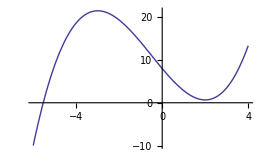

ερώτημα δ)

```mathematica
Clear["Global`*"]
f[x_]:=Sin[1/x]
g[x_]:=x*Sin[1/x]
Limit[f[x],x->0]
Limit[g[x],x->0]
```

Interval[{-1,1}]

0

```mathematica
Limit[f[x],x->0,Direction->1]
Limit[f[x],x->0,Direction->-1]
Limit[g[x],x->0,Direction->1]
Limit[g[x],x->0,Direction->-1]
```

Interval[{-1,1}]

Interval[{-1,1}]

0

0

Σύμφωνα με τις παρακάτω γραφικές παραστασεις το 1ο όριο δεν υπάρχει αφού κοντά στο 0 δεν μπορούμε να βρούμε ένα σημείο που να τείνει η γραφική παράσταση ενώ στο 2ο όριο παρατηρούμε ότι αυτός ο αριθμός είναι το 0.

```mathematica
Plot[f[x],{x,-0.1,0.1}]
```

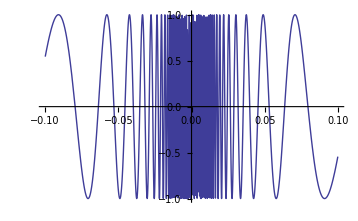

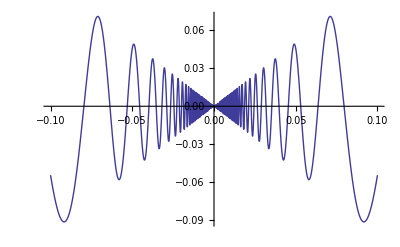

```mathematica
Plot[g[x],{x,-0.1,0.1}]
```

Ασκηση 2

ερώτημα α)  i)

```mathematica
Clear["Global`*"]
Integrate[Sqrt[Sin[x]]/(Sqrt[Sin[x]]+Sqrt[Cos[x]]),{x,0,Pi/2}]
```

π/4

```mathematica
Integrate[1/(Sqrt[9-x^2]),{x,0,3}]
```

π/2

```mathematica
Integrate[x^4*E^(-x^2),{x,0,Infinity}]
```

(3 √π)/8

ερώτημα α)  ii)

```mathematica
Sum[1/n^6,{n,1,Infinity}]
```

π^6/945

```mathematica
Sum[n^2,{n,1,N}]
```

1/6 N (1+N) (1+2 N)

```mathematica
Sum[1/(n!)^2,{n,0,Infinity}]
```

BesselI[0,2]

ερώτημα β)

Η μέθοδος του Νευτωνα για την εύρεση της 34 ρίζας του αριθμού 6.

```mathematica
Clear["Global`*"]
f[x_]=x^34-6;
f2[x_]=D[f[x],x];
x[0]=2;
ArithmosEpanalipseon=25;
Do[   x[n+1]=N[ x[n]-((f[x[n]])/(f2[x[n]])),400 ] , {n,0,ArithmosEpanalipseon}  ];

Lush=x/.FindRoot[f[x],{x,2},WorkingPrecision->400];
Sfalma[y_]:=Abs[Lush-x[y]];

values=Table[{n,N[x[n],20],N[Sfalma[n],5]},{n,1,ArithmosEpanalipseon}];
TableForm[values ,TableHeadings->{None,{"Επανάληψη","Αποτέλεσμα λύσης","Σφάλμα"}},TableAlignments->Center]
```

Επανάληψη | Αποτέλεσμα λύσης | Σφάλμα
1 | 1.9411764706087791744 | 0.88706
2 | 1.8840830450576593879 | 0.82997
3 | 1.8286688379974382376 | 0.77456
4 | 1.7748844608039311127 | 0.72077
5 | 1.7226819777196012242 | 0.66857
6 | 1.6720148635586124489 | 0.6179
7 | 1.6228379633882624743 | 0.56873
8 | 1.5751074553578040898 | 0.521
9 | 1.5287808198739579742 | 0.47467
10 | 1.483816823752699157 | 0.4297
11 | 1.4401755425180575271 | 0.38606
12 | 1.3978184829578064294 | 0.34371
13 | 1.3567089723064807663 | 0.3026
14 | 1.316813259472561854 | 0.2627
15 | 1.2781035197143885976 | 0.22399
16 | 1.240565942075895066 | 0.18645
17 | 1.2042223292217450342 | 0.15011
18 | 1.1691871606008955774 | 0.11508
19 | 1.1358143801880721891 | 0.081702
20 | 1.1050476216445273146 | 0.050936
21 | 1.0790790234498569623 | 0.024967
22 | 1.0616604837971026454 | 0.0075484
23 | 1.0549340307937780066 | 0.00082192
24 | 1.054122586066254879 | 0.000010479
25 | 1.0541121088007304017 | 1.7186×10^-9

Η μέθοδος του Νευτωνα για την εύρεση της 5 ρίζας του αριθμού 5.

```mathematica
Clear["Global`*"]
f[x_]=x^5-5;
f2[x_]=D[f[x],x];
x[0]=3;
ArithmosEpanalipseon=10;
Do[   x[n+1]=N[ x[n]-((f[x[n]])/(f2[x[n]])),400 ] , {n,0,ArithmosEpanalipseon}  ];

Lush=x/.FindRoot[f[x],{x,2},WorkingPrecision->400];
Sfalma[y_]:=Abs[Lush-x[y]];

values=Table[{n,N[x[n],20],N[Sfalma[n],5]},{n,1,ArithmosEpanalipseon}];
TableForm[values ,TableHeadings->{None,{"Επανάληψη","Αποτέλεσμα λύσης","Σφάλμα"}},TableAlignments->Center]
```

Επανάληψη | Αποτέλεσμα λύσης | Σφάλμα
1 | 2.412345679012345679 | 1.0326
2 | 1.9594050739364335269 | 0.57968
3 | 1.6353667533770078072 | 0.25564
4 | 1.448103758970908734 | 0.068374
5 | 1.3858886706644971273 | 0.006159
6 | 1.3797841610615583157 | 0.0000545
7 | 1.3797296657663651662 | 4.3052×10^-9
8 | 1.3797296614612148593 | 2.6867×10^-17
9 | 1.3797296614612148324 | 1.0463×10^-33
10 | 1.3797296614612148324 | 1.5869×10^-66

Ασκηση 3

ερώτημα α)

```mathematica
Clear["Global`*"]
f[x_]=2x^2+2x-3;
g[x_]=-x^2-2x+1;
Plot[{f[x],g[x]},{x,-3,3}]
```

Από την γραφική παράσταση παίρνουμε ότι τα κοινά σημεία είναι {-1.99,1.03}      {0.6699,-0.8024}

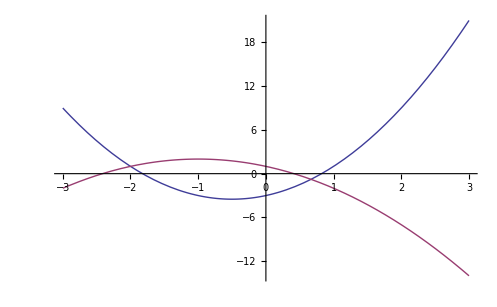

```mathematica
Solve[2x^2+2x-3==-x^2-2x+1,x]
```

{{x→-2},{x→2/3}}

```mathematica
f[-2] 
f[2/3]
```

1

-7/9

Με την Solve βρίσκουμε ότι τα κοινά σημεία είναι τα (-2,1)   (2/3,-7/9)

ερώτημα β)

```mathematica
NSolve[2x^2+2x-3==-x^2-2x+1,x]
```

{{x→-2.},{x→0.666667}}

```mathematica
h[x_]=f[x]-g[x];
FindRoot[h[x],{x,1}]
FindRoot[h[x],{x,-1}]
```

{x→0.666667}

{x→-2.}

Η μέθοδος Solve μας δίνει ακριβώς τα σημεία τομής των δύο συναρτήσεων ενώ με την NSolve παίρνουμε σχεδόν τέλεια προσέγγιση των σημείων τομής. Όπως και με την FindRoot. Αυτό συμβαίνει γιατί η μέθοδος υπολογίζει προσεγγιστικά τα σημεία τομής με αριθμιτηκές μεθόδους.

Ασκηση 4

ερώτημα α)

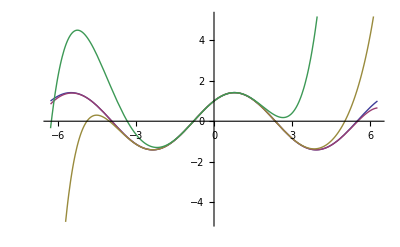

Τιμή | Σφάλμα p15 | Σφάλμα p10 | Σφάλμα p5
-5 | 0.00473718 | 1.49496 | 3.09075
-4 | 0.000148856 | 0.127215 | 1.69684
-3 | 1.64458×10^-6 | 0.0052491 | 0.481113
-2 | 2.72753×10^-9 | 0.0000583821 | 0.0587776
-1 | 4.4853×10^-14 | 2.69685×10^-8 | 0.00116868
0 | 0. | 0. | 0.
1 | 5.00711×10^-14 | 2.2816×10^-8 | 0.00156004
2 | 3.45599×10^-9 | 0.0000416496 | 0.106849
3 | 2.35202×10^-6 | 0.00313588 | 1.24887
4 | 0.000241105 | 0.0629329 | 6.94378
5 | 0.00873131 | 0.602146 | 25.4253

```mathematica
Clear["Global`*"]
f[x_]=Sin[x]+Cos[x];
p15[x_]=Normal[Series[f[x],{x,0,15}]];
p10[x_]=Normal[Series[f[x],{x,0,10}]];
p5[x_]=Normal[Series[f[x],{x,0,5}]];
Plot[{f[x],p15[x],p10[x],p5[x]},{x,-2*Pi,2*Pi}]
e15[x_]=Abs[f[x]-p15[x]]//N;
e10[x_]=Abs[f[x]-p10[x]]//N;
e5[x_]=Abs[f[x]-p5[x]]//N;
valuestable=Table[{i,e15[i],e10[i],e5[i]},{i,-5,5,1}];
TableForm[valuestable,TableHeadings->{None,{"Τιμή","Σφάλμα p15","Σφάλμα p10","Σφάλμα p5"}},TableAlignments->Center]
```

ερώτημα β)

```mathematica
Clear["Global`*"]
f[x_,Y_]=Sin[Sqrt[x^2+y^2]]/Sqrt[x^2+y^2];
Plot3D[f[x,y],{x,-8,8},{y,-8,8},PlotRange->All]
ContourPlot[f[x,y],{x,-8,8},{y,-8,8},PlotRange->All,PlotLegends->Automatic,ColorFunction->"BlueGreenYellow",Contours->20]
```

-Graphics3D-

-Graphics-

ερώτημα γ)

```mathematica
Clear["Global`*"]
ParametricPlot3D[{r*Cos[a],r*Sin[a],r^2},{r,0,1},{a,0,2Pi}]
ParametricPlot3D[{r*Cos[a],r*Sin[a],r*(1-r^2)},{r,0,1},{a,0,2Pi}]
ParametricPlot3D[{r*Cos[a],r*Sin[a],r*(1-r^2)},{r,0,1.5},{a,0,2Pi}]
ParametricPlot3D[{r*Cos[a],r*Sin[a],Sin[r]},{r,0,2Pi},{a,0,2Pi}]
ParametricPlot3D[{r*Cos[a],r*Sin[a],Cos[r]},{r,0,2Pi},{a,0,Pi}]
ParametricPlot3D[{r*Cos[a],r*Sin[a],E^(-r)},{r,0,1},{a,0,2Pi}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

Ασκηση 5

ερώτημα α)

Η λύση του συστήματος χρησιμοποιώντας τον τύπο S(t)=e^At S(0) :

```mathematica
Clear["Global`*"]
A=({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}});
S0={1,0,1};
S[t_]=MatrixExp[t*A].S0;
FullSimplify[S[t]]
```

{1/3 ⅇ^-t (1+2 ⅇ^(3 t)),2/3 ⅇ^-t (-1+ⅇ^(3 t)),1/3 ⅇ^-t (1+2 ⅇ^(3 t))}

ερώτημα β)

```mathematica
Clear["Global`*"]
A=Table[Max[i,j]+1,{i,8},{j,8}];
MatrixForm[A]
B=Eigenvalues[A];
N[Max[B],15]
N[Min[B],15]
```

(2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
3 | 3 | 4 | 5 | 6 | 7 | 8 | 9
4 | 4 | 4 | 5 | 6 | 7 | 8 | 9
5 | 5 | 5 | 5 | 6 | 7 | 8 | 9
6 | 6 | 6 | 6 | 6 | 7 | 8 | 9
7 | 7 | 7 | 7 | 7 | 7 | 8 | 9
8 | 8 | 8 | 8 | 8 | 8 | 8 | 9
9 | 9 | 9 | 9 | 9 | 9 | 9 | 9)

Η μέγιστη ιδιοτιμή του πίνακα A:

55.9366921858836

Η ελάχιστη ιδιοτιμή του πίνακα A:

-7.91950082065374

ερώτημα γ)

```mathematica
Clear["Global`*"]
Solve[x+2y+z==3 &&3x+2y+z==2 &&2x+y+2z==1,{x,y,z}]
```

{{x→-1/2,y→5/3,z→1/6}}

```mathematica
A={{1,2,1},{3,2,1},{2,1,2}};
B={3,2,1};
LinearSolve[A,B]
```

{-1/2,5/3,1/6}

Και στις δύο περιπτώσεις βρίσκουμε την ίδια λύση. 

Επαλήθευση λύσης:

Αρχικά βρίσκουμε την ορίζουσα του πίνακα Α:

```mathematica
Det[A]
```

-6

Η ορίζουσα του πίνακα δεν είναι 0 οπότε βρίσκουμε τον αντίστροφό του:

```mathematica
A2=Inverse[A];
```

Επιβεβαιώνουμε ότι η λύση είναι σωστή:

```mathematica
LUSH=A2.B
```

{-1/2,5/3,1/6}

Ασκηση 6

ερώτημα α)

```mathematica
Clear["Global`*"]
f[r_,a_,T_]:=NDSolve[{x'[t]==r*x[t]*(1-x[t]),x[0]==a},x,{t,0,T},WorkingPrecision->$MachinePrecision,PrecisionGoal->$MachinePrecision]

r1:=1/2
r2:=2
a1:=2/10
a2:=15/10

s1[t_]=x[t]/.f[r1,a1,20];
s2[t_]=x[t]/.f[r1,a2,20];
s3[t_]=x[t]/.f[r2,a1,20];
s4[t_]=x[t]/.f[r2,a2,20];

Plot[{s1[t],s2[t]},{t,0,20},PlotRange->{0,1.7}]  
Plot[{s3[t],s4[t]},{t,0,20},PlotRange->{0,1.7}]
```

Η γραφική παράσταση των λύσεων για  r=0.5 :

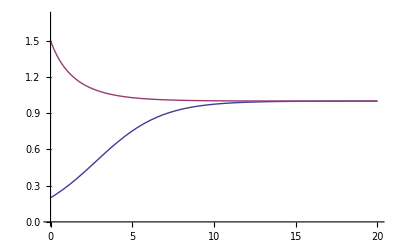

Η γραφική παράσταση των λύσεων για  r=2 :

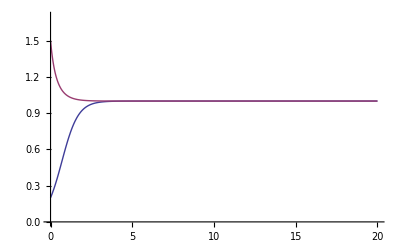

ερώτημα β)

```mathematica
g[r_,a_]:=DSolve[{x'[t]==r*x[t]*(1-x[t]),x[0]==a},x[t],t] 

s5[t_]=x[t]/.g[r1,a1];
s6[t_]=x[t]/.g[r1,a2];
s7[t_]=x[t]/.g[r2,a1];
s8[t_]=x[t]/.g[r2,a2];

Plot[{s5[t],s6[t],s7[t],s8[t]},{t,0,20},PlotRange->{0,1.7}]
```

Η γραφική παράσταση των λύσεων για  r=2, r=0.5 :

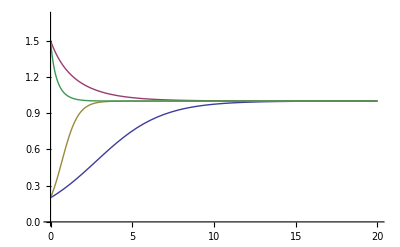

Η γραφική παράσταση των αριθμιτικών και των αναλυτικών λύσεων για  r=2, r=0.5. 
Παρατηρούμε ότι οι καμπύλες της αριθμιτικής λύσης με αυτές της αναλυτικής, βρίσκονται σχεδόν ακριβώς η μία πάνω στην άλλη :

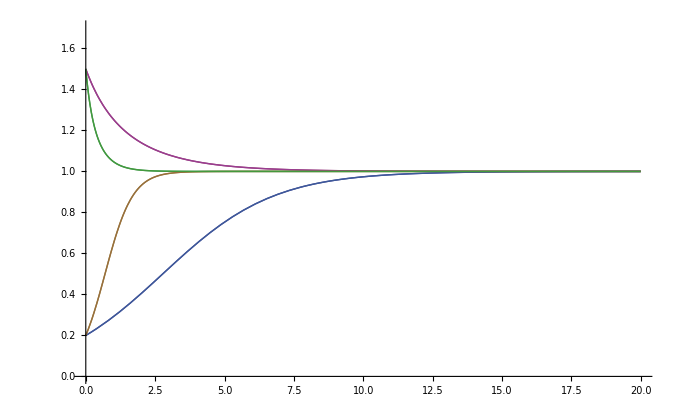

```mathematica
Plot[{s1[t],s2[t],s3[t],s4[t],s5[t],s6[t],s7[t],s8[t]},{t,0,20},PlotRange->{0,1.7}]
```

ερώτημα γ)

Ο πίνακας όταν x(0)=0.2 και r=0.5 :

```mathematica
Error[x_,y_]:=Abs[x-y]

ValuesTable1=Table[{i,s5[i],s1[i],Error[s5[i],s1[i]]},{i,0,2,0.1}];

TableForm[ValuesTable1,TableHeadings->{None,{"Τιμή","Αναλυτική Λύση","Αριθμιτική Λύση","Απόλυτο Σφάλμα"}},TableAlignments->Center]
```

Τιμή | Αναλυτική Λύση | Αριθμιτική Λύση | Απόλυτο Σφάλμα
0. | 0.2 | 0.2 | 0.
0.1 | 0.20812 | 0.20812 | 3.3406×10^-9
0.2 | 0.216481 | 0.216481 | 3.94159×10^-9
0.3 | 0.225082 | 0.225082 | 9.14154×10^-9
0.4 | 0.233922 | 0.233922 | 9.36344×10^-9
0.5 | 0.243001 | 0.243001 | 6.3724×10^-9
0.6 | 0.252317 | 0.252317 | 6.97478×10^-9
0.7 | 0.261866 | 0.261866 | 7.84259×10^-9
0.8 | 0.271645 | 0.271645 | 8.60742×10^-9
0.9 | 0.281649 | 0.281649 | 6.84244×10^-9
1. | 0.291875 | 0.291875 | 6.38544×10^-9
1.1 | 0.302316 | 0.302316 | 4.53508×10^-9
1.2 | 0.312965 | 0.312965 | 8.16482×10^-9
1.3 | 0.323815 | 0.323815 | 8.29798×10^-10
1.4 | 0.334858 | 0.334858 | 1.50895×10^-8
1.5 | 0.346085 | 0.346085 | 1.67302×10^-9
1.6 | 0.357486 | 0.357486 | 1.37472×10^-8
1.7 | 0.36905 | 0.36905 | 1.22246×10^-8
1.8 | 0.380767 | 0.380767 | 8.62252×10^-9
1.9 | 0.392624 | 0.392624 | 4.32611×10^-8
2. | 0.40461 | 0.40461 | 3.86183×10^-8

Ο πίνακας όταν x(0)=1.5 και r=2 :

```mathematica
ValuesTable2=Table[{i,s8[i],s4[i],Error[s8[i],s4[i]]},{i,0,2,0.1}];

TableForm[ValuesTable2,TableHeadings->{None,{"Τιμή","Αναλυτική Λύση","Αριθμιτική Λύση","Απόλυτο Σφάλμα"}},TableAlignments->Center]
```

Τιμή | Αναλυτική Λύση | Αριθμιτική Λύση | Απόλυτο Σφάλμα
0. | 1.5 | 1.5 | 0.
0.1 | 1.37535 | 1.37535 | 1.01391×10^-9
0.2 | 1.28773 | 1.28773 | 8.04985×10^-9
0.3 | 1.2239 | 1.2239 | 3.4037×10^-8
0.4 | 1.17616 | 1.17616 | 1.33464×10^-8
0.5 | 1.13977 | 1.13977 | 3.25032×10^-8
0.6 | 1.1116 | 1.1116 | 2.21409×10^-8
0.7 | 1.08956 | 1.08956 | 3.81074×10^-8
0.8 | 1.07215 | 1.07215 | 9.84507×10^-9
0.9 | 1.05831 | 1.05831 | 2.29486×10^-8
1. | 1.04724 | 1.04724 | 3.30728×10^-8
1.1 | 1.03835 | 1.03835 | 2.99952×10^-8
1.2 | 1.03118 | 1.03118 | 2.41223×10^-8
1.3 | 1.02539 | 1.02539 | 1.77233×10^-8
1.4 | 1.02069 | 1.02069 | 8.36096×10^-9
1.5 | 1.01688 | 1.01688 | 2.25038×10^-8
1.6 | 1.01377 | 1.01377 | 3.59239×10^-9
1.7 | 1.01125 | 1.01125 | 1.31125×10^-8
1.8 | 1.00919 | 1.00919 | 2.68757×10^-9
1.9 | 1.00751 | 1.00751 | 1.99815×10^-8
2. | 1.00614 | 1.00614 | 1.79651×10^-8

Ασκηση 7

```mathematica
Clear["Global`*"]
f[a_,T_]:=NDSolve[{x''[t]==-x[t]^5,x[0]==a,x'[0]==0},x,{t,0,T}]
s1=f[1,25];
s2=f[2,25];
s3=f[0.8,30];
s4=f[1.6,30];
Plot[{x[t]/.s1,x[t]/.s2},{t,0,25}]
Plot[{x[t]/.s3,x[t]/.s4},{t,0,30}]
```

Παρατηρούμε ότι ο διπλασιασμός του α οδηγεί σε υποτετραπλασιασμό του Τ.

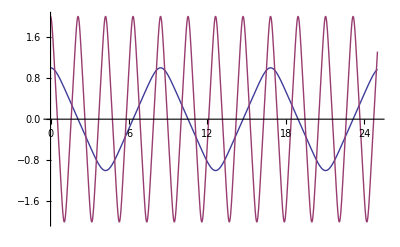

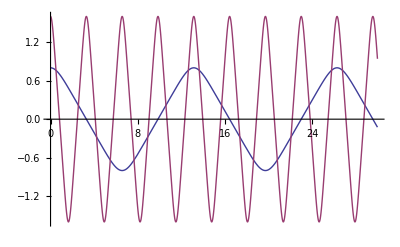

Θα βρούμε την σχέση μεταξύ του Τ και του α μέσω της σχέσης (5) σελ.139:

```mathematica
Τ[a_]=Integrate[1/(Sqrt[2*((1/6)*a^6-(1/6)*x^6)]),{x,-a,a}]//N;
FullSimplify[Τ[a],a>0]
```

Βρίσκουμε ότι Τ=4.20655 / a^2 . Οπότε επαληθεύουμε ότι ο διπλασιασμός του α οδηγεί σε υποτετραπλασιασμό του Τ.

4.20655/a^2

Για την επίδραση της τριβής:

```mathematica
g[a_,c_,T_]:=NDSolve[{x''[t]==-x[t]^5-c*x'[t],x[0]==a,x'[0]==0},x,{t,0,T}]
s5=x[t]/.g[0.9,0.02,600];
Plot[s5,{t,0,600},PlotRange->All]
```

Παρατηρούμε ότι η επίδραση της τριβής μειώνει το πλάτος α κατά συνέπεια αυξάνεται η περίοδος Τ.

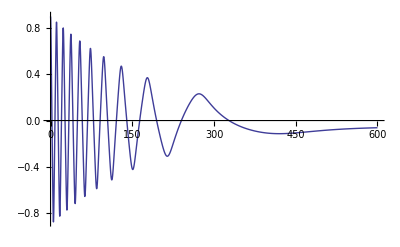

Ασκηση 8

ερώτημα α)

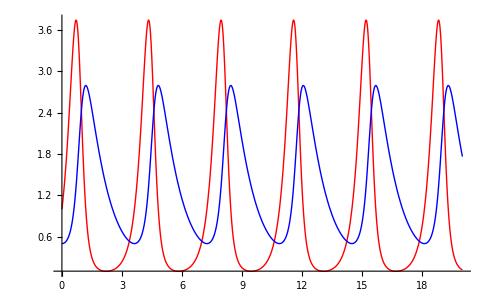

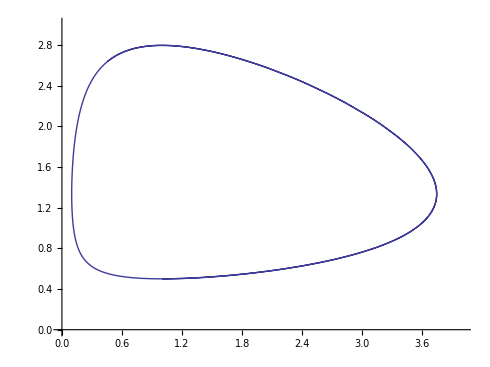

```mathematica
Clear["Global`*"]
f[a_,p_,b_,q_,StartX_,StartY_,T_]:=NDSolve[{x'[t]== x[t]*(a-p*y[t]),y'[t]==y[t]*(q*x[t]-b),x[0]==StartX,y[0]==StartY},{x,y},{t,0,T}]

s=f[4,3,1,1,1,0.5,20];

Plot[{x[t]/.s,y[t]/.s},{t,0,20},PlotRange->All,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]

ParametricPlot[{x[t],y[t]}/.s,{t,0,5},PlotRange->{{0,4},{0,3}}]
```

ερώτημα β)

i)  Από το πρώτο διάγραμμα με την βοήθεια του Get Coordinates για το θήραμα βρίσκουμε μέγιστο {{0.6908,3.722}} και ελάχιστο {{2.202, 0.09842}} 

Οπότε για το θήραμα έχουμε περίπου:

Μέγιστος πληθισμός 3.700 ο οποίος παρουσιάζεται πρώτη φορά σε 70 μέρες.
Ελάχιστος πληθισμός 100 ο οποίος παρουσιάζεται πρώτη φορά σε 220 μέρες.

Αναλόγως για τον θηρευτή έχουμε περίπου:

Μέγιστος πληθισμός 2.700 ο οποίος παρουσιάζεται πρώτη φορά σε 120 μέρες.
Ελάχιστος πληθισμός 500 ο οποίος παρουσιάζεται πρώτη φορά σε 0 μέρες.

ii)  Από το δεύτερο διάγραμμα παρατηρούμε ότι η τροχιά του συστήματος στο xy επίπεδο είναι κλειστή οπότε το φαινόμενο είναι περιοδικό. 
Από το πρώτο διάγραμμα μπορούμε να καταλάβουμε ότι η περίοδος είναι περίπου 3.6 δηλαδή 360 ημέρες.

ερώτημα γ)

Υπολογίζουμε ακριβώς τις τιμές των μεγίστων και ελαχίστων καθώς και τους χρόνους στους οποίους συμβαίνουν.
Παρατηρούμε ότι οι προσεγγιστικές τιμές που βρήκαμε στο β) ερώτημα είναι πολύ κοντά στις πραγματικές τιμές.

```mathematica
FindMaximum[x[t]/.s,{t,0}]
FindMinimum[x[t]/.s,{t,1}]
FindMaximum[y[t]/.s,{t,1}]
FindMinimum[y[t]/.s,{t,0.01}]
```

{3.74328,{t→0.708383}}

{0.0977256,{t→2.20878}}

{2.79431,{t→1.19193}}

{0.5,{t→-7.44375×10^-9}}